# from http://arxiv.org/pdf/quant-ph/0211066.pdf

```mathematica
(*0.78 micron waist for 980 nm*)
```

```mathematica
Clear["Global`*"]
λtrap=980 10^-9;
c=299792458;
λ01=852.34727582 10^-9; (*D2 line*)
λ02=894.59295986 10^-9; (*D1 line*)
ℏ=1.054571726 10^-34;
kB =1.3806488 10^-23 ;
ω01= 2π  c/λ01;(*D2 line*)
ω02= 2π  c/λ02;
w0= 0.78 10^-4; (*waist in cm*)
Δλ1=λ01-λtrap;(*-ve for red detuning*)
Δλ2=λ02-λtrap;(*-ve for red detuning*)

Δ1=Δλ1/λ01 ω01;
Δ2=Δλ2/λ02 ω02;

Γ=2π 5.2227 10^6;
p=1;(*in mW*)

Δ=3/(1/Δ1+2/Δ2);
I0=1.1 ;(*i sat in mW/cm^2*)
Udip=(ℏ Γ)/2 p/(π w0^2 I0)Γ/Δ;

TrapTemp=Udip/kB 1000 (*in mK/mW*)
Udip/ℏ
```

-0.845702

-1.1072×10^8

```mathematica
f= 4;
inuc=7/2;
j=f-inuc;

(Δ2-Δ1)/(Δ2+2Δ1)(f(f+1)-inuc(inuc+1)+j(j+1))/(f(f+1))
```

-0.0376473

# TLS

```mathematica
Clear["Global`*"]
c=299792458;
λ0=852.34727582 10^-9;
ℏ=1.054571726 10^-34;
kB =1.3806488 10^-23 ;
ω0= 2π  c/λ0;
Δλ=λ0-935.6 10^-9;
w0= 0.78 10^-6; (*waist*)
Δ=Abs[Δλ/λ0 ω0];
Γ=2π 5.2227 10^6;
p=1 10^-3;
i=p/(π (w0/2)^2);
Udip=(3π c^2)/(2 ω0^3)Γ/Δ i;
Γscat=(3π c^2)/(2 ℏ ω0^3)(Γ/Δ)^2 i;
TrapTemp=Udip/kB 1000 (*in mK/mW*)
Γscat/2/π
```

0.904227

2.86427

# with the Fine structure splitting (correction to trap depth)

```mathematica
Clear["Global`*"]
c=299792458;
λ01=852.34727582 10^-9; (*D2 line*)
λ02=894.59295986 10^-9; (*D1 line*)
ℏ=1.054571726 10^-34;
kB =1.3806488 10^-23 ;
ω01= 2π  c/λ01;(*D2 line*)
ω02= 2π  c/λ02;

P=0;(*+/-1 for circ. pol. trap light*)
gF=1/4;
mF=1;

λTrap=980 10^-9;
w0=0.78 10^-6; (*waist*)
ωTrap = 2π c/λTrap;

Δ=Abs[(ω01+ω02)/2-ωTrap];
ΔFS=Abs[ω01-ω02];
Γ=2π 5.2227 10^6;
p=1 10^-3;
i=p/(π (w0/2)^2);
Udip=(3π c^2)/(2 ω01^3)Γ/Δ(1+1/3 P gF mF ΔFS/Δ)i;
TrapTempmW=Udip/kB 1000(*in mW*)
```

0.828159

```mathematica
LightShift=(Udip 2)/(2π ℏ 10^6)(*of the ground state, in MHz--this is NOT the light shift of the transition, so kind of uselesss*)
```

34.5121

```mathematica
TrapTempmW 3.1
```

2.56729

# phot. detection rate in mot + trap

```mathematica
p=10;(*of each cooling beam, in mW*)
i=p/((π 1.5^2)/100);(*using 6mm 4σ dia--> 3mm 2σ, 1.5mm beam radius*)
Δapp = 10;(*cooling beams are already red detuned by 10 MHz from 4->5' transition, in MHz*)
c=299792458;
λ01=852.34727582 10^-9; (*D2 line*)
λ02=894.59295986 10^-9; (*D1 line*)
ℏ=1.054571726 10^-34;
kB =1.3806488 10^-23 ;
ω01= 2π  c/λ01;(*D2 line*)

Δ=( LightShift +Δapp); (*regular freq. in MHz; additional detuning due to dipole trap light shift*)
Γ= 5.2227; (*regular freq. in MHz for Cs D2*)
iSAT=2.7059; (*mW/cm^2 for Cs D2*)

Rsc=Γ/2(i/iSAT)/(1+4(Δ/Γ)^2+i/iSAT) (*photon scattering rate in MHz*)
```

0.703088

```mathematica
(*from http://en.wikipedia.org/wiki/Steradian I calculated NA = 0.55 to be about 0.842 sr solid angle *)
```

```mathematica
photCountRate=0.842/(4π)Rsc 10^6 (*in s^-1*)
```

47109.8

# phot detection rate in mot only (no trap)

```mathematica
Rsc=Γ/2(i/iSAT)/(1+4(Δapp/Γ)^2+i/iSAT)
```

2.00933

```mathematica
photCountRate=0.842/(4π)Rsc 10^6 (*in s^-1*)
```

134633.

# want to maximize this : (photons scattered by atom in dip trap : photons scattered by atom in MOT only) Note that there will be many more atoms scattering from backgrd than from inside the dipole trap, and this only compares one atom in dipole trap vs one atom in MOT. At such high intensities (1000 Isat), you may get other deleterious effects like heating with only marginal improvements in SNR

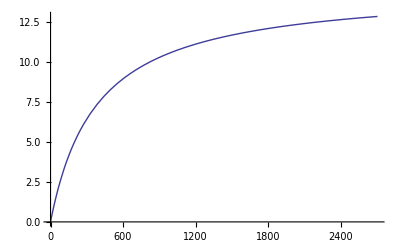

```mathematica
Plot[1/(1+4(Δ/Γ)^2+ii/iSAT) /(1/(1+4(Δapp/Γ)^2 ii/iSAT)),{ii,0,1000iSAT}]
```